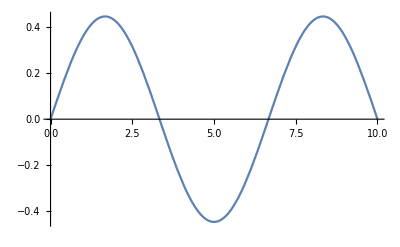

```mathematica
ψ[x_,nx_]:=√(2/L)*Sin[(nx*π)/L x];

L=10;

Plot[ψ[x,3],{x,0,10}]
```

```mathematica
Manipulate[Plot[ψ[x,nx]^2,{x,0,10},PlotLegends->{nx}],{nx,1,100,1},ControlType->Slider]
```